# QNM Package Testing

## Load from Kernel directory

```mathematica
QNMDir=ExpandFileName[FileNameJoin[{NotebookDirectory[],"..","Kernel","QNM.wl"}]];
Get[QNMDir];
```

## QNM frequencies from https://arxiv.org/pdf/2202.03837

```mathematica
data={{"(s,n,l,m)", "a", "Mω","_sΛ_l^m"},
{"(-2,0,2,2)","0","0.3736716 − 0.0889623ⅈ","4"},
{"(-2,0,2,2)","0.7","0.5326002 − 0.0807928ⅈ","2.9032 + 0.1832ⅈ"},
{"(-2,0,2,-2)","99/100","0.2921067 − 0.0880523ⅈ","4.7163 − 0.1966ⅈ"},
{"(-2,0,2,0)","99/100","0.4236846 − 0.0727008ⅈ", "3.9102 + 0.0319ⅈ"},
{"(-2,0,3,3)","99/100","1.3230831 − 0.029403ⅈ","6.4040 + 0.1043ⅈ"}};
```

```mathematica
dataTable=Grid[data,Frame->All,
ItemStyle->{Automatic,{Directive[Bold,FontSize->14]}},Background->{Automatic,{Lighter[Gray,0.9]}},Spacings->{1,1} ];
```

```mathematica
Labeled[dataTable,"Values from 2202.03837, Table 1",Top,LabelStyle->Directive[Bold, FontSize->16]]
```

(s,n,l,m) | a | Mω | _sΛ_l^m
(-2,0,2,2) | 0 | 0.3736716 − 0.0889623ⅈ | 4
(-2,0,2,2) | 0.7 | 0.5326002 − 0.0807928ⅈ | 2.9032 + 0.1832ⅈ
(-2,0,2,-2) | 99/100 | 0.2921067 − 0.0880523ⅈ | 4.7163 − 0.1966ⅈ
(-2,0,2,0) | 99/100 | 0.4236846 − 0.0727008ⅈ | 3.9102 + 0.0319ⅈ
(-2,0,3,3) | 99/100 | 1.3230831 − 0.029403ⅈ | 6.4040 + 0.1043ⅈValues from 2202.03837, Table 1

## Computed QNM frequencies

```mathematica
ClearAll[qnmdata,qnmvalues]
qnmdata = {{"(s,n,l,m)", "a", "Mω","_sΛ_l^m"}};
qnmvalues={{-2,2,2,0},{-2,2,2,0.7},{-2,2,-2,99/100},{-2,2,0,99/100},{-2,3,3,99/100}};
```

```mathematica
For[i=1,i<=Length[qnmvalues],i++,
args = StringJoin["(",StringRiffle[ToString/@qnmvalues[[i,1;;3]],","],")"];
λ = QNMFrequency@@qnmvalues[[i]];
AppendTo[qnmdata,{args,qnmvalues[[i]][[4]],NumberForm[λ["QNMfrequency"],{7,7}], NumberForm[λ["SeparationConstant"],{4,4}]}];
];
```

Calculating QNMFrequency with tolerance 1.×10^-6 for 100 gridpoints.

Calculating QNMFrequency with tolerance 1.×10^-6 for 100 gridpoints.

Calculating QNMFrequency with tolerance 1.×10^-6 for 100 gridpoints.

«2 more identical outputs»

```mathematica
qnmTable=Grid[qnmdata,Frame->All,
ItemStyle->{Automatic,{Directive[Bold,FontSize->14]}},Background->{Automatic,{Lighter[Gray,0.9]}},Spacings->{1,1} ];
```

```mathematica
Labeled[qnmTable,"Calculated Values",Top,LabelStyle->Directive[Bold, FontSize->16]]
```

(s,n,l,m) | a | Mω | _sΛ_l^m
(-2,2,2) | 0 | 0.3736711-0.0889602 ⅈ | 4
(-2,2,2) | 0.7 | 0.5326009-0.0807926 ⅈ | 2.9030+0.1832 ⅈ
(-2,2,-2) | 99/100 | 0.2921073-0.0880523 ⅈ | 4.7160-0.1966 ⅈ
(-2,2,0) | 99/100 | 0.4236854-0.0727006 ⅈ | 3.9100+0.0319 ⅈ
(-2,3,3) | 99/100 | 0.9795426-0.1018119 ⅈ | 7.5490+0.3144 ⅈCalculated Values

## Radial QNM Profiles

```mathematica
result =QNMMode[-2,2,2,0.7,"Coordinates"->"Hyperboloidal"];
Subscript[ψ, s]=result["QNMRadialProfile"];
```

Computing QNMMode with tolerance 1.×10^-6 resolution 100 and coordinates Hyperboloidal

Calculating QNMFrequency with tolerance 1.×10^-6 for 100 gridpoints.

Power::infy: Infinite expression 1/0. encountered.

Height function: {Indeterminate,-6844.79,-1732.56,-783.635,-450.348,-295.365,-210.691,-159.283,-125.652,-102.388,-85.5802,-73.0083,-63.3327,-55.7069,-49.5738,-44.555,-40.3855,-36.8755,-33.886,-31.3131,-29.0782,-27.1204,-25.3923,-23.8566,-22.4832,-21.2479,-20.1311,-19.1165,-18.1907,-17.3425,-16.5625,-15.8426,-15.1762,-14.5574,-13.9812,-13.4434,-12.9401,-12.4682,-12.0247,-11.6072,-11.2135,-10.8415,-10.4896,-10.1562,-9.83988,-9.53945,-9.25378,-8.98187,-8.72281,-8.47577,-8.24002,-8.01487,-7.79972,-7.594,-7.39719,-7.20882,-7.02847,-6.85574,-6.69025,-6.53168,-6.37971,-6.23405,-6.09445,-5.96066,-5.83244,-5.70959,-5.5919,-5.47921,-5.37134,-5.26812,-5.16942,-5.0751,-4.98502,-4.89908,-4.81715,-4.73914,-4.66495,-4.5945,-4.52768,-4.46444,-4.4047,-4.34839,-4.29544,-4.2458,-4.19943,-4.15626,-4.11625,-4.07936,-4.04556,-4.01481,-3.98708,-3.96233,-3.94056,-3.92173,-3.90583,-3.89284,-3.88275,-3.87555,-3.87123,-3.8698}

DeltaTilde: {1.,0.999706,0.998826,0.997359,0.995309,0.992679,0.989471,0.985691,0.981345,0.976437,0.970976,0.964969,0.958425,0.951353,0.943762,0.935664,0.927069,0.917991,0.908441,0.898432,0.887979,0.877096,0.865797,0.854097,0.842013,0.829561,0.816757,0.803618,0.790162,0.776405,0.762365,0.748061,0.73351,0.718732,0.703743,0.688564,0.673211,0.657704,0.642062,0.626303,0.610445,0.594506,0.578506,0.562461,0.54639,0.530311,0.51424,0.498196,0.482194,0.466253,0.450387,0.434612,0.418946,0.403402,0.387996,0.372742,0.357654,0.342747,0.328033,0.313524,0.299235,0.285176,0.271359,0.257796,0.244497,0.231472,0.218732,0.206285,0.194141,0.182308,0.170795,0.159609,0.148758,0.138248,0.128086,0.118279,0.108833,0.0997521,0.0910425,0.0827088,0.0747557,0.0671873,0.0600075,0.0532201,0.0468284,0.0408354,0.0352441,0.0300571,0.0252768,0.0209052,0.0169444,0.013396,0.0102616,0.00754245,0.00523976,0.00335447,0.00188733,0.000838956,0.00020976,-2.22045×10^-16}

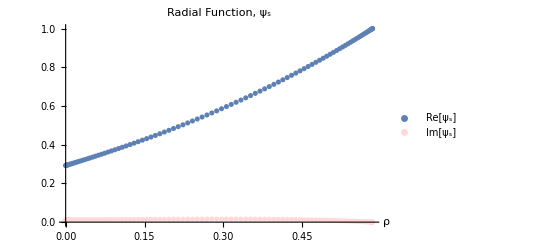

```mathematica
Show[ListPlot[Subscript[ψ, s]//Re,PlotRange->All,PlotLegends->Placed[LineLegend[{"Re[ψ_s]"}],Automatic]],ListPlot[Table[{ Subscript[ψ, s][[i,1]],Subscript[ψ, s][[i,2]]//Im},{i,1,Length[Subscript[ψ, s]]}],PlotStyle->LightRed,PlotRange->All,PlotLegends->Placed[LineLegend[{"Im[ψ_s]"}],Automatic]],
PlotLabel->"Radial Function, ψ_s",
LabelStyle->{FontSize->14},
AxesLabel->{"ρ"," "}]
```